Note: In this problem set, expressions in green cells match corresponding expressions in the text answers.

```mathematica
Clear["Global`*"]
```

1.  The net of roads in the figure connecting four villages is to be reduced to minimum length, but so that one can still reach every village from every other village. Which of the roads should be retained? Find the solution (a) by inspection, (b) by Dijkstra’s algorithm.

What I need to do is to plot the graph, including edge weights, which represent the distances in this case.

```mathematica
Clear["Global`*"]
```

```mathematica
lis={{0,0},{4,2},{1.7,0},{3.4,0}}
```

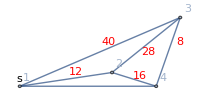

```mathematica
g3=Graph[{1<->2,2<->3,3<->4,1<->3,2<->4,1<->4},VertexLabels->"Name",VertexCoordinates->{{0,0},{2.3,0.4},{4,2},{3.4,0}},EdgeWeight->{12,28,8,40,16,36},Epilog->{{Text[Style["s",Medium],{0,0.2}]},{Red,Text[Style["12",Medium],{1.4,0.4}]},{Red,Text[Style["16",Medium],{3,0.3}]},{Red,Text[Style["28",Medium],{3.2,1}]},{Red,Text[Style["40",Medium],{2.2,1.3}]},{Red,Text[Style["8",Medium],{4,1.3}]},{Red,Text[Style["36",Medium],{1.8,-0.2}]}},ImageSize->200,ImagePadding->10]
```

The weighted adjacency matrix is a good thing to think about, though I don’t use it here. Using matrix form lets me see it better, but I understand I can’t calculate with this form. If I want to calculate with the matrix for some operation, I need to get the sparse matrix form, which is what I get when I don’t specify matrix form.

```mathematica
wam=WeightedAdjacencyMatrix[g3]
```

SparseArray[<12>, {4, 4}]

```mathematica
%//MatrixForm
```

(0 | 12 | 40 | 36
12 | 0 | 28 | 16
40 | 28 | 0 | 8
36 | 16 | 8 | 0)

```mathematica
am=AdjacencyMatrix[g3]
```

SparseArray[<12>, {4, 4}]

```mathematica
%//MatrixForm
```

(0 | 1 | 1 | 1
1 | 0 | 1 | 1
1 | 1 | 0 | 1
1 | 1 | 1 | 0)

After looking at the documentation for awhile, I see that what I need is the command FindSpanningTree, because in the case of a weighted graph, the path of minimum total weights is returned, which is exactly what I want.

```mathematica
FindSpanningTree[g3];
HighlightGraph[g3,%,GraphHighlightStyle->"Thick"]
```

-Graphics-

```mathematica
size[g_]:=With[{edges=EdgeList[FindSpanningTree[{g,1}]]},Total[PropertyValue[{g,#},EdgeWeight]&/@edges]]
N[size[g3]]
```

36.

The spanning tree shown above and the sum of edge weights agree with the answer in the text.

Find shortest tour is an interesting command, but not quite the thing for this.

```mathematica
FindShortestTour[g3]
```

{76,{1,3,4,2,1}}

To try to get a better grasp, I’m modifying the problem slightly and doing it again.

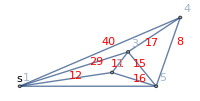

```mathematica
g4=Graph[{1<->2,2<->3,3<->4,4<->5,1<->4,2<->5,1<->5,3<->5,1<->3},VertexLabels->"Name",VertexCoordinates->{{0,0},{2.3,0.4},{2.7,1},{4,2},{3.4,0}},EdgeWeight->{12,11,17,8,40,16,36,15,29},Epilog->{{Text[Style["s",Medium],{0,0.2}]},{Red,Text[Style["12",Medium],{1.4,0.3}]},{Red,Text[Style["16",Medium],{3,0.2}]},{Red,Text[Style["17",Medium],{3.3,1.25}]},{Red,Text[Style["11",Medium],{2.45,0.65}]},{Red,Text[Style["40",Medium],{2.2,1.3}]},{Red,Text[Style["8",Medium],{4,1.3}]},{Red,Text[Style["36",Medium],{1.8,-0.2}]},{Red,Text[Style["29",Medium],{1.9,0.7}]},{Red,Text[Style["15",Medium],{3,0.65}]}},ImageSize->200,ImagePadding->10]
```

```mathematica
FindSpanningTree[g4];
HighlightGraph[g4,%,GraphHighlightStyle->"Thick"]
```

-Graphics-

I’m glad I did this alternative version of the problem. It shows that FindShortestPath doesn’t really solve it. In both approaches there are four necessary edges to the road system graph. But in the FindShortestPath method I am forced to manually choose from a set of edges inside curly braces and probably get 2-5 instead of 3-5, making the total road length 47 instead of 46. After a search, I found an automated way to add up the edge lengths and display the total:

```mathematica
size[g_]:=With[{edges=EdgeList[FindSpanningTree[{g,1}]]},Total[PropertyValue[{g,#},EdgeWeight]&/@edges]]
N[size[g4]]
```

46.

4 - 9 Dijkstra’s algorithm
For each graph find the shortest paths.

5. Problem represented by a diagram.

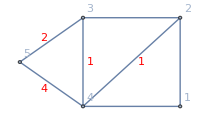

```mathematica
g5=Graph[{1<->2,2<->3,3<->4,4<->5,3<->5,2<->4,1<->4},VertexLabels->"Name",VertexCoordinates->{{0,0},{0,2},{-2,2},{-2,0},{-3.3,1}},EdgeWeight->{2,3,1,4,2,1,5},Epilog->{{Text[Style["s",Medium],{0,-0.15}]},{Red,Text[Style["1",Medium],{-0.8,1}]},{Red,Text[Style["2",Medium],{0.15,1}]},{Red,Text[Style["1",Medium],{-1.85,1}]},{Red,Text[Style["3",Medium],{-0.9,2.15}]},{Red,Text[Style["5",Medium],{-1,-0.18}]},{Red,Text[Style["4",Medium],{-2.8,0.4}]},{Red,Text[Style["2",Medium],{-2.8,1.55}]}},ImageSize->200,ImagePadding->10]
```

The problem description was a little vague. There are shortest paths for individual vertices, but I don’t understand what the shortest path for the entire graph would mean. If what is wanted is the shortest path for lowest to highest numbered vertex, or 1-2-4-3-5, this is the first entry on the last row of the grid below. The grid is kind of a matrix that tells the shortest path from any vertex to any other vertex.

```mathematica
Grid[Table[FindShortestPath[g5,m,n,Method->"Dijkstra"],{n,1,5},{m,1,5}],Frame->All]
```

{1} | {2,1} | {3,4,2,1} | {4,2,1} | {5,3,4,2,1}
{1,2} | {2} | {3,4,2} | {4,2} | {5,3,4,2}
{1,2,4,3} | {2,4,3} | {3} | {4,3} | {5,3}
{1,2,4} | {2,4} | {3,4} | {4} | {5,3,4}
{1,2,4,3,5} | {2,4,3,5} | {3,5} | {4,3,5} | {5}

```mathematica
FindSpanningTree[g5];
HighlightGraph[g5,%,GraphHighlightStyle->"Thick"]
```

-Graphics-

```mathematica
size[g_]:=With[{edges=EdgeList[FindSpanningTree[{g,1}]]},Total[PropertyValue[{g,#},EdgeWeight]&/@edges]]
N[size[g5]]
```

6.

The above graph plot and cell gets what the text answer wants. The text answer is: (1,2), (2,4), (3,4), (3,5); L_2=2, L_3=4, L_4=3, L_5=6. The first half of the answer recites the edge sequence pictured above. The second half is an accumulated tally of getting from vertex 1 to each numerically superior vertex.

7. Problem represented by a diagram.

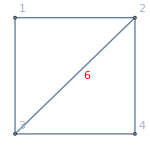

```mathematica
g7=Graph[{1<->2,2<->3,3<->4,4<->2,1<->3},VertexLabels->"Name",VertexCoordinates->{{0,0},{2,0},{0,-2},{2,-2}},EdgeWeight->{10,6,2,3,17},Epilog->{{Text[Style["s",Medium],{-0.1,-0.1}]},{Red,Text[Style["17",Medium],{-0.12,-1}]},{Red,Text[Style["10",Medium],{1,0.12}]},{Red,Text[Style["6",Medium],{1.2,-1}]},{Red,Text[Style["3",Medium],{2.1,-1}]},{Red,Text[Style["2",Medium],{1,-2.15}]}},ImageSize->150,ImagePadding->10]
```

```mathematica
FindSpanningTree[g7];
HighlightGraph[g7,%,GraphHighlightStyle->"Thick"]
```

-Graphics-

```mathematica
size[g_]:=With[{edges=EdgeList[FindSpanningTree[{g,1}]]},Total[PropertyValue[{g,#},EdgeWeight]&/@edges]]
N[size[g7]]
```

15.

The edges highlighted above are the ones shown in the text answer.

9. Problem represented by a diagram.

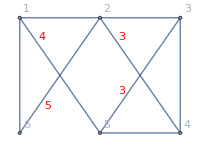

```mathematica
g6=Graph[{1<->2,2<->3,3<->4,4<->5,1<->6,1<->5,2<->4,3<->5,2<->6},VertexLabels->"Name",VertexCoordinates->{{0,0},{2,0},{4,0},{4,-3},{2,-3},{0,-3}},EdgeWeight->{10,2,1,6,15,4,3,3,5},Epilog->{{Text[Style["s",Medium],{-0.15,-0.15}]},{Red,Text[Style["10",Medium],{1,0.15}]},{Red,Text[Style["2",Medium],{3,0.15}]},{Red,Text[Style["4",Medium],{0.55,-0.5}]},{Red,Text[Style["3",Medium],{2.55,-0.5}]},{Red,Text[Style["5",Medium],{0.7,-2.3}]},{Red,Text[Style["3",Medium],{2.55,-1.9}]},{Red,Text[Style["6",Medium],{3,-3.25}]},{Red,Text[Style["1",Medium],{4.15,-1.5}]},{Red,Text[Style["15",Medium],{-0.22,-1.5}]}},ImageSize->200,ImagePadding->10]
```

```mathematica
g6ew={10,2,1,6,15,4,3,3,5}
```

{10,2,1,6,15,4,3,3,5}

Again the grid gives the shortest path from any vertex to any other vertex.

```mathematica
Grid[Table[FindShortestPath[g6,m,n,Method->"Dijkstra"],{n,1,6},{m,1,6}],Frame->All]
```

{1} | {2,3,5,1} | {3,5,1} | {4,3,5,1} | {5,1} | {6,2,3,5,1}
{1,5,3,2} | {2} | {3,2} | {4,2} | {5,3,2} | {6,2}
{1,5,3} | {2,3} | {3} | {4,3} | {5,3} | {6,2,3}
{1,5,3,4} | {2,4} | {3,4} | {4} | {5,3,4} | {6,2,4}
{1,5} | {2,3,5} | {3,5} | {4,3,5} | {5} | {6,2,3,5}
{1,5,3,2,6} | {2,6} | {3,2,6} | {4,2,6} | {5,3,2,6} | {6}

```mathematica
FindSpanningTree[g6];
HighlightGraph[g6,%,GraphHighlightStyle->"Thick"]
```

-Graphics-

```mathematica
size[g_]:=With[{edges=EdgeList[FindSpanningTree[{g,1}]]},Total[PropertyValue[{g,#},EdgeWeight]&/@edges]]
N[size[g6]]
```

15.

The edges shown above are the ones listed in the text.